# Simulate consumer-resource models with externally-supplied resources

```mathematica
ClearAll["Global`*"]
$HistoryLength = 0;
```

```mathematica
AbioticCRM[parameters_Association, simulation_Association] := Module[{
	
	M = parameters["M"],
	S = parameters["S"],
    ρ = parameters["ρ"],
    μc = parameters["μc"],
    σc = parameters["σc"],
    μg = parameters["μg"],
    σg = parameters["σg"],
    μd = parameters["μd"],
    σd = parameters["σd"],
    μb = parameters["μb"],
    σb = parameters["σb"],
    μo = parameters["μo"],
    σo = parameters["σo"],
    
    tEnd = simulation["tEnd"],
    
    growth,
    consumption,
    death,
    influx,
    outflux,
    dRNdtAbiotic,
    
    simulatedDynamics,
    resourceProperties,
    consumerProperties,
    
    output

	},
	
	dRNdtAbiotic[t_] := Module[{},

	{Resource'[t] == influx - outflux*Resource[t] - Resource[t]*(consumption.Species[t]) + 10^-8,
	 Species'[t] == Species[t]*(growth.Resource[t] - death) + 10^-8}

	];
	
	{growth, consumption} = GenerateGrowthConsumption[M, S, μg, σg, μc, σc, ρ];
	death = μd + σd*RandomVariate[NormalDistribution[], S];
	influx = μb + σb*RandomVariate[NormalDistribution[], M];
	outflux = μo + σo*RandomVariate[NormalDistribution[], M];
	
	simulatedDynamics = SimulateDynamics[dRNdtAbiotic, M, S, tEnd];
	
	If[simulatedDynamics["ResourceDynamics"] === $Failed,
		(output = Join[simulatedDynamics, AssociationMap[$Failed &, {"phiR", "Rmean", "Rfluct", "phiN", "Nmean", "Nfluct"}]];),
		(resourceProperties = CommunityProperties[simulatedDynamics["ResourceDynamics"][[-1]]];
		consumerProperties = CommunityProperties[simulatedDynamics["ConsumerDynamics"][[-1]]];
	
		output = Join[simulatedDynamics, AssociationThread[{"phiR", "Rmean", "Rfluct", "phiN", "Nmean", "Nfluct"},
														   Join[resourceProperties, consumerProperties]]])
	];
	
	output
	
	(*resourceProperties = CommunityProperties[simulatedDynamics[[1]][[1]][[-1]]];
	consumerProperties = CommunityProperties[simulatedDynamics[[1]][[2]][[-1]]];
	
	output = Join[simulatedDynamics, resourceProperties, consumerProperties];
	
	output*)
];

BioticCRM[parameters_Association, simulation_Association] := Module[{
	
	M = parameters["M"],
	S = parameters["S"],
    ρ = parameters["ρ"],
    μc = parameters["μc"],
    σc = parameters["σc"],
    μg = parameters["μg"],
    σg = parameters["σg"],
    μd = parameters["μd"],
    σd = parameters["σd"],
    μb = parameters["μb"],
    σb = parameters["σb"],
    
    tEnd = simulation["tEnd"],
    
    growth,
    consumption,
    death,
    influx,
    
    dRNdtBiotic,
    
    simulatedDynamics,
    resourceProperties,
    consumerProperties,
    
    output

	},
	
	dRNdtBiotic[t_] := Module[{},

	{Resource'[t] == Resource[t]*(influx - Resource[t] -  consumption.Species[t]) + 10^-8,
	 Species'[t] == Species[t]*(growth.Resource[t] - death) + 10^-8}

	];
	
	{growth, consumption} = GenerateGrowthConsumption[M, S, μg, σg, μc, σc, ρ];
	death = μd + σd*RandomVariate[NormalDistribution[], S];
	influx = μb + σb*RandomVariate[NormalDistribution[], M];
	
	simulatedDynamics = SimulateDynamics[dRNdtBiotic, M, S, tEnd];
	
	If[simulatedDynamics["ResourceDynamics"] === $Failed,
		(output = Join[simulatedDynamics, AssociationMap[$Failed &, {"phiR", "Rmean", "Rfluct", "phiN", "Nmean", "Nfluct"}]];),
		(resourceProperties = CommunityProperties[simulatedDynamics["ResourceDynamics"][[-1]]];
		consumerProperties = CommunityProperties[simulatedDynamics["ConsumerDynamics"][[-1]]];
	
		output = Join[simulatedDynamics, AssociationThread[{"phiR", "Rmean", "Rfluct", "phiN", "Nmean", "Nfluct"},
														   Join[resourceProperties, consumerProperties]]])
	];
	
	output
	
];

GenerateGrowthConsumption[M_, S_, μg_, σg_, μc_, σc_, ρ_] := Module[{
		xC,
		xG,
		growth,
		consumption},
		
		xC = RandomVariate[NormalDistribution[0, 1], {M, S}]; 
		xG = RandomVariate[NormalDistribution[0, 1], {S, M}]; 
		
		growth = μg/M+σg/(√M)*xG;
		consumption = μc/M+σc/(√M)*(ρ*Transpose[xG] + √(1 - ρ^2)*xC);
		
		{growth, consumption}
	];
	
SimulateDynamics[dRNdt_, M_, S_, tEnd_] := Module[{

		SolveODE,
		
		initR,
	    initN,
	    initRPerturbed,
	    initNPerturbed,
	 
	    solution,
	    solutionPerturbed,
	    tLast,
	    tLastP,
	    evaluatedSolution,
	    evaluatedSolutionPerturbed,
	    distanceTrajectory,
	    maxLE,
	    output},
	    
	    SolveODE[initResource_, initConsumer_] := Module[{sol, status},
	    
	    sol = Quiet[TimeConstrained[NDSolve[Join[dRNdt[t],
													 {Resource[0] == initResource, Species[0] == initConsumer,
													 WhenEvent[Max[Abs[Resource[t]], Abs[Species[t]]] > 10^6, "StopIntegration"]}],
											   {Resource, Species},
											   {t, 0, tEnd},
											   Method -> "StiffnessSwitching", AccuracyGoal -> 7, PrecisionGoal -> 7, MaxSteps -> 1000],
									120, $Failed]];
	    
	    sol
	    
	    ];
	    
	    initR = RandomVariate[UniformDistribution[{10^-8, 2/M}], M];
		initN = RandomVariate[UniformDistribution[{10^-8, 2/S}], S];
						   
		solution = SolveODE[initR, initN];
						   
		If[solution === $Failed,
			(output = <|"ResourceDynamics" -> $Failed, "ConsumerDynamics" -> $Failed, "EndTime" -> $Failed, "maxLe" -> $Failed|>),
			(tLast = solution[[1, 1, 2]]["Domain"][[1, 2]];
			
			evaluatedSolution = <|"ResourceDynamics" -> Table[Evaluate[Resource[t]/.solution[[1]]], {t, Subdivide[0, tLast, 200]}],
							      "ConsumerDynamics" -> Table[Evaluate[Species[t]/.solution[[1]]], {t, Subdivide[0, tLast, 200]}]|> // Quiet;
							 
			initRPerturbed = initR + 10^-6;
			initNPerturbed = initN + 10^-6;
		
			solutionPerturbed = SolveODE[initRPerturbed, initNPerturbed];
			
			If[solutionPerturbed === $Failed,
				(output = Join[evaluatedSolution, <|"EndTime" -> tLast, "maxLe" -> $Failed|>]),
				(
				evaluatedSolutionPerturbed = {Table[Evaluate[Resource[t]/.solutionPerturbed[[1]]], {t, Subdivide[0, tLast, 200]}],
										  Table[Evaluate[Species[t]/.solutionPerturbed[[1]]], {t, Subdivide[0, tLast, 200]}]} // Quiet;
									  
				distanceTrajectory = Log[10, MapThread[EuclideanDistance, {Join[evaluatedSolution["ResourceDynamics"],
																			    evaluatedSolution["ConsumerDynamics"], 2],
																			Join[evaluatedSolutionPerturbed[[1]], evaluatedSolutionPerturbed[[2]], 2]}]];					
		
				maxLE = LinearModelFit[Transpose[{Subdivide[0, tLast, 200], distanceTrajectory}], {1, x}, x]["BestFitParameters"][[2]];
							 					 
				output = Join[evaluatedSolution, <|"EndTime" -> tLast, "maxLe" -> maxLE|>])]
	
		)];
	
	output
	
	];
	
CommunityProperties[abundances_] := Module[{
	
		phiA,
		Amean,
		Afluct},
		
		phiA = N[Count[abundances, x_ /; x > 10^-4]/Length[abundances]];
		Amean = Mean[abundances];
		Afluct = Mean[abundances^2];
		
		{phiA, Amean, Afluct}
		
	];
```

```mathematica
StabilitySimulation[filename_, model_, parameterSets_Association, simulation_Association, nRep_: 20] := Module[{

    tEnd = simulation["tEnd"],
    
    FormatParams,
    
    varyingParams,
    fixedParams,
    paramNames,
    paramRanges,
    allCombinations,
    maxLEs,
    dataTemp,
    oldKeys,
    newKeys,
    output},
    
    FormatParams[params_Association] := Join[KeyDrop[params, {"μinteract", "σinteract"}], 
										         <|"μc" -> params["μinteract"], "σc" -> params["σinteract"], "μg" -> params["μinteract"], "σg" -> params["σinteract"]|>];
	
	varyingParams = Select[parameterSets, Length[#] > 0 &];
    fixedParams = Select[parameterSets, Length[#] === 0 &];
    
    paramNames = Keys[varyingParams];
    paramRanges = Values[varyingParams];
    allCombinations = Tuples[paramRanges];
    
    LaunchKernels[];
	DistributeDefinitions[StabilityParmSet, AbioticCRM, BioticCRM, SimulateDynamics, GenerateGrowthConsumption, CommunityProperties,
						 FormatParams];
    ParallelEvaluate[Off[Set::shape]];
    
    maxLEs = ParallelTable[Module[{paramSet},
								  paramSet = FormatParams[Join[fixedParams, AssociationThread[paramNames, parmcombo]]];
								  StabilityParmSet[model, paramSet, tEnd, nRep]],
						   {parmcombo, allCombinations}] // Quiet;
						   
	ParallelEvaluate[On[Set::shape]];
	
	dataTemp = Dataset[Flatten[maxLEs, 1]];
	oldKeys = Keys[Normal[dataTemp][[1]]];
	newKeys = oldKeys /. {"ρ" -> "rho", "μc" -> "mu_c", "σc" -> "sigma_c", 
	                      "μg" -> "mu_g", "σg" -> "sigma_g", "μd" -> "mu_d", 
	                      "σd" -> "sigma_d", "μb" -> "mu_b", "σb" -> "sigma_b",
	                      "μo" -> "mu_o", "σo" -> "sigma_o"};
	output = Dataset[Map[AssociationThread[newKeys, Values[#]] &, Normal[dataTemp]]];
	
	Export[filename, output, "CSV"];
];

StabilityParmSet[model_, paramSet_Association, tEnd_, nRep_] := Module[{
    
		CRM,
		maxLeParmSet},
		
		CRM = Switch[model, "Abiotic", AbioticCRM, "Biotic",  BioticCRM];
		
		maxLeParmSet = Table[Join[paramSet, KeyDrop[CRM[paramSet, <|"tEnd" -> tEnd|>],
					                                {"ResourceDynamics", "ConsumerDynamics", "EndTime"}]],
						{n, 1, nRep}] // Quiet;
			                 
		maxLeParmSet
											
	];
```

```mathematica
StabilitySimulation["C:/Users/jamil/Documents/PhD/Data/external_resource_stability/simulations/rho_vs_sigma_complete(mathematica).csv",
					"Abiotic",
					<|"M" -> 150, "S" -> 150,
					  "ρ" -> Range[0.65, 0.95, 0.1], "μinteract" -> 1.0, "σinteract" -> Range[0.1, 4.5, 0.2],
					  "μd" -> 1.0, "σd" -> 0.1,
					  "μb" -> 1.0, "σb" -> 0.1,
					  "μo" -> 1.0, "σo" -> 0.0|>, <|"tEnd" -> 200|>, 30] // Quiet;
```

```mathematica
StabilitySimulation["C:/Users/jamil/Documents/PhD/Data/external_resource_stability/simulations/rho_vs_sigma_biotic.csv",
					"Biotic",
					<|"M" -> 150, "S" -> 150,
					  "ρ" -> Range[0.5, 1.0, 0.05], "μinteract" -> 3.0, "σinteract" -> Range[0.3, 1.5, 0.05],
					  "μd" -> 1.0, "σd" -> 0.1,
					  "μb" -> 1.0, "σb" -> 0.1|>,
					  <|"tEnd" -> 400|>, 30] // Quiet;
```

```mathematica
StabilitySimulation["C:/Users/jamil/Documents/PhD/Data/external_resource_stability/simulations/rho_vs_sigma_abiotic.csv",
					"Abiotic",
					<|"M" -> 150, "S" -> 150,
					  "ρ" -> Range[0.5, 1.0, 0.05], "μinteract" -> 3.0, "σinteract" -> Range[0.3, 1.5, 0.05],
					  "μd" -> 1.0, "σd" -> 0.1,
					  "μb" -> 1.0, "σb" -> 0.1,
					  "μo" -> 1.0, "σo" -> 0.0|>,
					  <|"tEnd" -> 400|>, 30] // Quiet;
```

```mathematica
ρtest = 1.0;
μtest = 3.0;
σtest = 0.8;

paramTestA = <|"M" -> 150, "S" -> 150, "ρ" -> ρtest, "μc" -> μtest, "σc" -> σtest, "μg" -> μtest, "σg" -> σtest,
			  "μd" -> 1.0, "σd" -> 0.1, "μb" -> 1.0, "σb" -> 0.1, "μo" -> 1.0, "σo" -> 0.0|>;
			  
paramTestB = <|"M" -> 150, "S" -> 150, "ρ" -> ρtest, "μc" -> μtest, "σc" -> σtest, "μg" -> μtest, "σg" -> σtest,
			  "μd" -> 1.0, "σd" -> 0.1, "μb" -> 1.0, "σb" -> 0.1|>;

simulationTestA = AbioticCRM[paramTestA, <|"tEnd" -> 500|>];
simulationTestB = BioticCRM[paramTestB, <|"tEnd" -> 500|>];
```

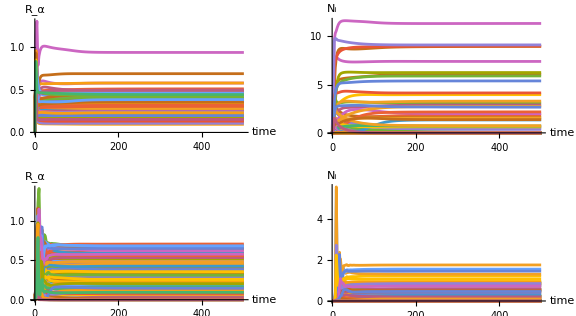

```mathematica
RdynamicsA = Table[simulationTestA["ResourceDynamics"][[ All, alpha]], {alpha, 1, Length[simulationTestA["ResourceDynamics"][[1, All]]]}];
NdynamicsA = Table[simulationTestA["ConsumerDynamics"][[All, alpha]], {alpha, 2, Length[simulationTestA["ConsumerDynamics"][[1, All]]]}];
RdynamicsB = Table[simulationTestB["ResourceDynamics"][[ All, alpha]], {alpha, 1, Length[simulationTestB["ResourceDynamics"][[1, All]]]}];
NdynamicsB = Table[simulationTestB["ConsumerDynamics"][[All, alpha]], {alpha, 2, Length[simulationTestB["ConsumerDynamics"][[1, All]]]}];

Show[GraphicsGrid[{{ListLinePlot[RdynamicsA, AxesLabel->{"time", "R_α"}, DataRange->{0, simulationTestA["EndTime"]}, AspectRatio->0.5, PlotRange -> All], 
				  ListLinePlot[NdynamicsA, AxesLabel->{"time", "N_i"}, DataRange->{0, simulationTestA["EndTime"]}, AspectRatio->0.5, PlotRange -> All]},
				  {ListLinePlot[RdynamicsB, AxesLabel->{"time", "R_α"}, DataRange->{0, simulationTestB["EndTime"]}, AspectRatio->0.5, PlotRange -> All], 
				  ListLinePlot[NdynamicsB, AxesLabel->{"time", "N_i"}, DataRange->{0, simulationTestB["EndTime"]}, AspectRatio->0.5, PlotRange -> All]}}], 
	ImageSize->Large]
```

```mathematica
Print[simulationTestA[["Nmean"]], " ", simulationTestA[["Nfluct"]]]
```

0.728319 4.44644

```mathematica
df = Import["C:/Users/jamil/Documents/PhD/Data/external_resource_stability/simulations/rho_vs_sigma_complete(mathematica).csv", "Dataset"];

df2 = df[All, Function[row,
    Append[row, AssociationThread[
        {"maxLe", "phiR", "Rmean", "Rfluct", "phiN", "Nmean", "Nfluct"} -> ToExpression[row["maxLe"]]
    ]]
]]

df3 = df2[All, Map[N[#, MachinePrecision] &, #] &];
Export["C:/Users/jamil/Documents/PhD/Data/external_resource_stability/simulations/rho_vs_sigma_complete(mathematica).csv", df3, "CSV"];
```